```mathematica
Examples of Electric fields E and corresponding vector potentials A:
```

```mathematica
Definition of the electric field profiles:
```

```mathematica
Ramp[t_,t0_]:=(1/2-3/4*Cos[π*t/t0]+1/4*Cos[π*t/t0]^3)

Ef[t_,A_,ω_,t0_,τ_]:=A*Cos[ω*(t-t0)]*Exp[-((t-t0)^2)/(2*τ^2)]
Econstant[t_,A_,t0_,t1_]:=A*HeavisideTheta[t-t0]*HeavisideTheta[t1-t]
Esmooth[t_,A_,t0_,t1_]:=A*Ramp[t,t0]*HeavisideTheta[t0-t]+Econstant[t,A,t0,t1]
Ecos[t_,A_,Ω_,t0_]:= A*Cos[Ω*(t-t0)]
Ecos1[t_,A_,Ω_,t0_]:= A*(1+Cos[Ω*(t-t0)])
```

```mathematica
Get the corresponding vector potential by indefinite integration :
```

```mathematica
FullSimplify[Integrate[Ef[t,A,ω,t0,τ],t]]
FullSimplify[Integrate[Econstant[t,A,t0,t1],t]]
FullSimplify[Integrate[Esmooth[t,A,t0,t1],t]]
FullSimplify[Integrate[Ecos[t,A,Ω,t0],t]]
FullSimplify[Integrate[Ecos1[t,A,Ω,t0],t]]
```

1/2 A ⅇ^(-1/2 τ^2 ω^2) √(π/2) τ (Erf[(t-t0-ⅈ τ^2 ω)/(√2 τ)]+Erf[(t-t0+ⅈ τ^2 ω)/(√2 τ)])

A HeavisideTheta[t-t0] (t-t0+(-t+t1) HeavisideTheta[t-t1]+(t0-t1) HeavisideTheta[t0-t1])

1/(48 π)A (24 π (t+(t-t0) HeavisideTheta[t-t0]+2 (-t+t1) HeavisideTheta[t-t0,t-t1]+2 (t0-t1) HeavisideTheta[t-t0,t0-t1])+27 t0 (-1+HeavisideTheta[t-t0]) Sin[(π t)/t0]-t0 (-1+HeavisideTheta[t-t0]) Sin[(3 π t)/t0])

(A Sin[(t-t0) Ω])/Ω

A (t+Sin[(t-t0) Ω]/Ω)

```mathematica
Copy/Paste Vector potential to new functions:
```

```mathematica
Af[t_,A_,ω_,t0_,τ_]:=1/2 A ⅇ^(-1/2 τ^2 ω^2) √(π/2) τ (Erf[(t-t0-ⅈ τ^2 ω)/(√2 τ)]+Erf[(t-t0+ⅈ τ^2 ω)/(√2 τ)])
Aconstant[t_,A_,t0_,t1_]:=A HeavisideTheta[t-t0] (t-t0+(-t+t1) HeavisideTheta[t-t1]+(t0-t1) HeavisideTheta[t0-t1])
Asmooth[t_,A_,t0_,t1_]:=1/(48 π)A (24 π (t+(t-t0) HeavisideTheta[t-t0]+2 (-t+t1) HeavisideTheta[t-t0,t-t1]+2 (t0-t1) HeavisideTheta[t-t0,t0-t1])+27 t0 (-1+HeavisideTheta[t-t0]) Sin[(π t)/t0]-t0 (-1+HeavisideTheta[t-t0]) Sin[(3 π t)/t0])
Acos[t_,A_,Ω_,t0_]:=(A Sin[(t-t0) Ω])/Ω
Acos1[t_,A_,Ω_,t0_]:=A (t+Sin[(t-t0) Ω]/Ω)
```

```mathematica
Plot  of impulse - like profile :
```

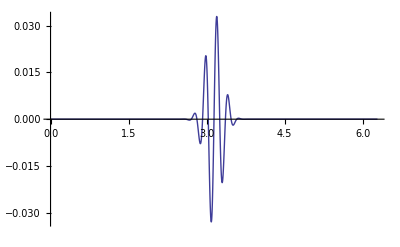

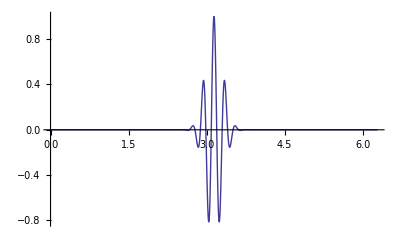

```mathematica
Plot[Re[Af[x,1,30,π,1.0/(2π)]],{x,0,2π},PlotRange->Full]
Plot[Ef[x,1,30,π,1.0/(2π)],{x,0,2π},PlotRange->Full]
```

```mathematica
Plot of the constant profile :
```

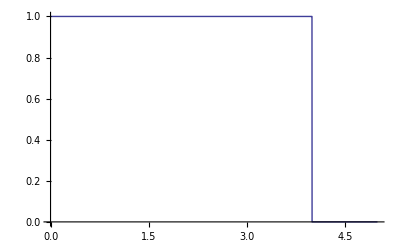

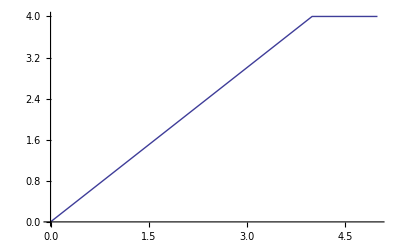

```mathematica
Plot[Econstant[x,1,0,4],{x,0,5},PlotRange->Full]
Plot[Re[Aconstant[x,1,0,4]],{x,0,5},PlotRange->Full]
```

```mathematica
Plot of the ramp profile :
```

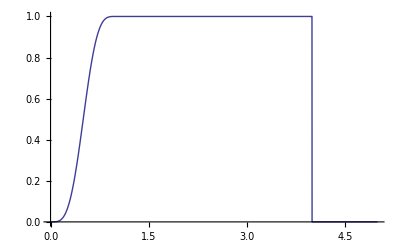

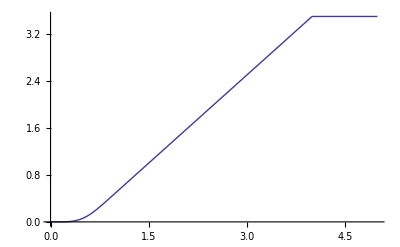

```mathematica
Plot[Esmooth[x,1,1,4],{x,0,5},PlotRange->Full]
Plot[Re[Asmooth[x,1,1,4]],{x,0,5},PlotRange->Full]
```

```mathematica
Plot of the Cos profile :
```

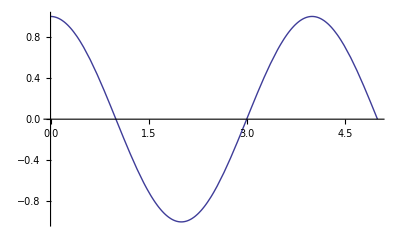

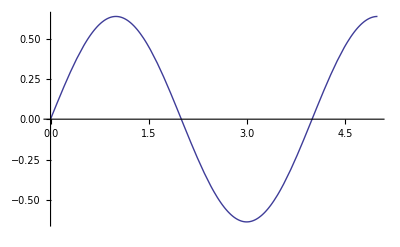

```mathematica
Plot[Ecos[x,1,π/2,0],{x,0,5},PlotRange->Full]
Plot[Re[Acos[x,1,π/2,0]],{x,0,5},PlotRange->Full]
```

```mathematica
Plot of the Cos profile :
```

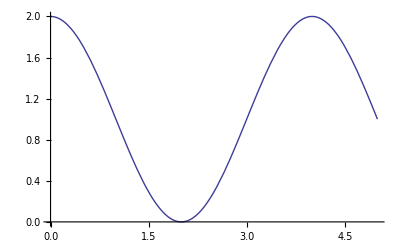

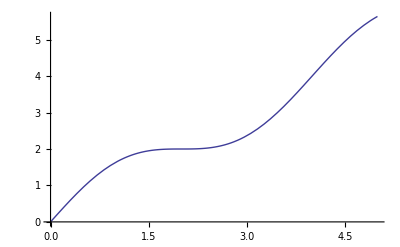

```mathematica
Plot[Ecos1[x, 1, π/2, 0], {x, 0, 5}, PlotRange -> Full]
Plot[Re[Acos1[x, 1, π/2, 0]], {x, 0, 5}, PlotRange -> Full]
```